# Project Coding Template APPM 2350 : Spring 2017 Authors: This student That student The student

Hi everyone!
The purpose of this document is to show you how a Mathematica notebook can be organized for easier legibility. It might make it is easier to understand the flow of your work this way.

For the 1st project I recommend copying the coaster template code into the first section below and starting by reviewing the Crash Course file!

```mathematica
Clear["Global`*"]
```

## Section 3: Observers at three different latitudes

Some text here to explain the following code (notice the brackets on the right→ side of the page!)
Also use SHIFT ENTER to evaluate code. If it goes blue to black, then it’s been saved.

```mathematica
Θ[t_] := -0.41 * Cos[(2π*t)/ 365.25]
```

```mathematica
x[t_,ϕ_] := Cos[ϕ] * Sin[2π*t]
```

```mathematica
y[t_,ϕ_] := -Cos[ϕ] * Cos[2π*t] * Cos[Θ[t]] + Sin[ϕ] * Sin[Θ[t]]
```

```mathematica
z[t_, ϕ_] := Cos[ϕ] * Cos[2π * t] * Sin[Θ[t]] + Sin[ϕ] * Cos[Θ[t]]
```

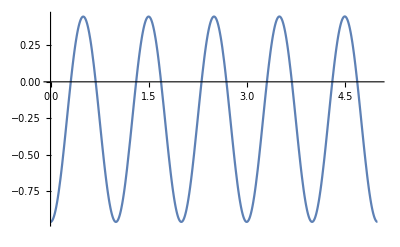

```mathematica
Plot[{y[t,0.698132]},{t,0,5}]
```

```mathematica
days ={t} /. Table[FindRoot[y[t,0.698132]==0, {t, day -0.25}], {day, 0.5, 365,0.5}]; 
riseIndex = 1;
setIndex = 2;
rise = 0;
set = 0;
dayLengths = {};

(*creates a list of day lengths *)
While[riseIndex < 730, 
rise = Part[days,riseIndex]; 
set = Part[days, setIndex]; 
AppendTo[dayLengths,(set-rise)];
 riseIndex = riseIndex+2; setIndex = setIndex+2]

(*some tests + printing min and max*)
dayLengths
Length[dayLengths]
Max[dayLengths]
Position[dayLengths,Max[dayLengths]]
Min[dayLengths]
Position[dayLengths,Min[dayLengths]]

(* find the closest absolute distance to .5 *)
findEquinox[loopStart_,loopEnd_] :=(
candidate = 0;
currentMin =1;
For[i=loopStart, i < loopEnd, i++,
candidate = Part[dayLengths,i];
currentMin = If[(Abs[.5 - candidate]) < (Abs[.5-currentMin]), candidate, currentMin]
]
Return[currentMin];
)
equinox = findEquinox[1,180];
```

{{0.381178},{0.381219},{0.381302},{0.381426},{0.381591},{0.381797},{0.382044},{0.382332},{0.382661},{0.383029},{0.383438},{0.383886},{0.384373},{0.3849},{0.385465},{0.386069},{0.38671},{0.387388},{0.388103},{0.388855},{0.389643},{0.390465},{0.391323},{0.392215},{0.39314},{0.394099},{0.39509},{0.396112},{0.397166},{0.398251},{0.399365},{0.400509},{0.401681},{0.402882},{0.404109},{0.405364},{0.406644},{0.40795},{0.40928},{0.410635},{0.412013},{0.413414},{0.414836},{0.416281},{0.417746},{0.419231},{0.420736},{0.42226},{0.423802},{0.425362},{0.42694},{0.428533},{0.430143},{0.431769},{0.433409},{0.435063},{0.436732},{0.438413},{0.440108},{0.441815},{0.443533},{0.445263},{0.447004},{0.448755},{0.450516},{0.452286},{0.454065},{0.455853},{0.457649},{0.459453},{0.461264},{0.463082},{0.464907},{0.466738},{0.468574},{0.470417},{0.472264},{0.474116},{0.475972},{0.477832},{0.479696},{0.481564},{0.483434},{0.485307},{0.487183},{0.489061},{0.49094},{0.492821},{0.494703},{0.496586},{0.49847},{0.500354},{0.502237},{0.504121},{0.506003},{0.507885},{0.509766},{0.511644},{0.513521},{0.515396},{0.517268},{0.519138},{0.521004},{0.522867},{0.524725},{0.52658},{0.52843},{0.530276},{0.532116},{0.53395},{0.535779},{0.537601},{0.539417},{0.541225},{0.543026},{0.544819},{0.546604},{0.54838},{0.550147},{0.551904},{0.553651},{0.555388},{0.557113},{0.558827},{0.56053},{0.562219},{0.563896},{0.565559},{0.567208},{0.568843},{0.570463},{0.572067},{0.573654},{0.575225},{0.576778},{0.578314},{0.579831},{0.581328},{0.582806},{0.584263},{0.5857},{0.587114},{0.588507},{0.589876},{0.591221},{0.592543},{0.593839},{0.59511},{0.596354},{0.597571},{0.598761},{0.599923},{0.601056},{0.602159},{0.603232},{0.604274},{0.605285},{0.606264},{0.60721},{0.608123},{0.609002},{0.609846},{0.610656},{0.61143},{0.612168},{0.61287},{0.613534},{0.614161},{0.61475},{0.615301},{0.615813},{0.616286},{0.616719},{0.617113},{0.617466},{0.617779},{0.618052},{0.618284},{0.618475},{0.618624},{0.618733},{0.6188},{0.618826},{0.61881},{0.618753},{0.618655},{0.618516},{0.618335},{0.618114},{0.617851},{0.617548},{0.617205},{0.616821},{0.616398},{0.615935},{0.615433},{0.614892},{0.614312},{0.613694},{0.613039},{0.612347},{0.611618},{0.610853},{0.610052},{0.609216},{0.608346},{0.607441},{0.606504},{0.605533},{0.60453},{0.603496},{0.60243},{0.601334},{0.600209},{0.599054},{0.597872},{0.596661},{0.595423},{0.594159},{0.592869},{0.591554},{0.590214},{0.588851},{0.587465},{0.586055},{0.584625},{0.583172},{0.5817},{0.580207},{0.578695},{0.577164},{0.575615},{0.574048},{0.572465},{0.570865},{0.569249},{0.567619},{0.565973},{0.564313},{0.56264},{0.560953},{0.559254},{0.557543},{0.55582},{0.554086},{0.552342},{0.550587},{0.548822},{0.547049},{0.545266},{0.543475},{0.541676},{0.539869},{0.538056},{0.536235},{0.534408},{0.532575},{0.530736},{0.528892},{0.527043},{0.52519},{0.523332},{0.52147},{0.519605},{0.517736},{0.515864},{0.51399},{0.512114},{0.510235},{0.508355},{0.506474},{0.504591},{0.502708},{0.500825},{0.498941},{0.497057},{0.495174},{0.493292},{0.49141},{0.489531},{0.487652},{0.485776},{0.483902},{0.482031},{0.480163},{0.478298},{0.476437},{0.474579},{0.472726},{0.470878},{0.469035},{0.467196},{0.465364},{0.463538},{0.461718},{0.459905},{0.458099},{0.456301},{0.454511},{0.45273},{0.450957},{0.449194},{0.44744},{0.445697},{0.443965},{0.442243},{0.440533},{0.438836},{0.437151},{0.435479},{0.433821},{0.432177},{0.430548},{0.428934},{0.427336},{0.425755},{0.424191},{0.422644},{0.421115},{0.419606},{0.418115},{0.416645},{0.415195},{0.413767},{0.412361},{0.410977},{0.409617},{0.40828},{0.406968},{0.405681},{0.40442},{0.403186},{0.401979},{0.400799},{0.399648},{0.398527},{0.397434},{0.396373},{0.395342},{0.394343},{0.393377},{0.392443},{0.391543},{0.390677},{0.389845},{0.389049},{0.388288},{0.387564},{0.386876},{0.386225},{0.385612},{0.385038},{0.384501},{0.384004},{0.383546},{0.383128},{0.382749},{0.38241},{0.382113},{0.381855},{0.381639},{0.381463},{0.381329},{0.381236},{0.381184}}

365

0.618826

{{183,1}}

0.381178

{{1,1}}

```mathematica
RiseAngle[dayRA_,phiRA_] := 
(srtRA = FindRoot[y[tRA, phiRA] == 0, {tRA, Round[dayRA] -0.75}];
180*ArcCos[n[tRA/.srtRA,phiRA]]/Pi)
```

```mathematica
boulderRA = Table[RiseAngle[dayRA,40*Pi/180],{dayRA,0,365,1}];
```

## Section II: Honey Badgers

Explaining more code

```mathematica
g[x_]=f'[x];
h[x_]=a-2g[x];
Plot[h[x],{x,-1,1},
PlotLabel->Style["Hello Out There!",Large],
AxesLabel->{"X label (meters)","Y label (meters)"},
ImageSize->Large]
```

-Graphics-

### Sub-Section Analysis

```mathematica
FindRoot[h[x],{x,0.1}]
```

FindRoot::nlnum: The function value {a-2. f'[0.1]} is not a list of numbers with dimensions {1} at {x} = {0.1}.

FindRoot[h[x],{x,0.1}]

A little more text, just for good measure.